Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: 11159

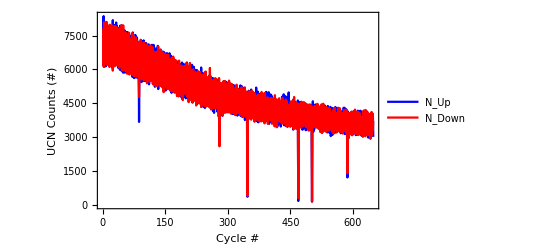

Number of Cycles: 679.

```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum=11159];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadata=ReadList[StringJoin[AscDir,"/",IntegerString[runNum,10,6],"/",IntegerString[runNum,10,6],"_Meta3.edm"],metaStructure2];
EDAListPlot[metadata[[2;;650,27]],metadata[[2;;650,28]],PlotLegends->{"N_Up","N_Down"},PlotStyle->{Blue,Red,Gray},Joined->True,PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"Cycle #","UCN Counts (#)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000}]
Print["Number of Cycles: ",maxCy=metadata[[-1]][[2]]];
```

```mathematica
Monitor[
Clear[data,histdata2];
data={};
For[runi=47,runi≤116,runi++,
If[runi≠ 20&&runi≠22,
data=Join[data,ReadList[StringJoin[AscDir,"\\",IntegerString[runNum,10,6],"\\",IntegerString[runNum,10,6],"_UCNdet_",IntegerString[runi,10,3],"_0001.fast.ascii"],metaStructure]];
];
];,ProgressIndicator[runi/10,ImageSize->{1000,100}]];
dimdata=Dimensions[data][[1]]
Dimensions[data]
```

8857142

{8857142,7}

## Studying timing difference between events

8857141

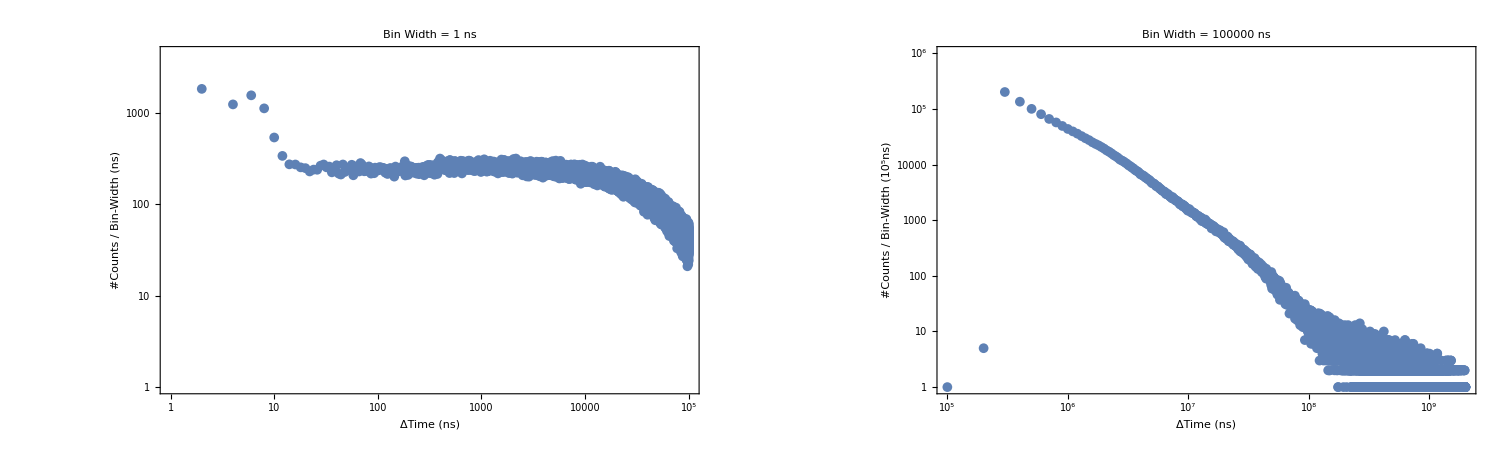

01_011369_timeStructure.png

```mathematica
tmdiff=(data[[2;;dimdata,4]]-data[[1;;dimdata-1,4]]);
Dimensions[tmdiff][[1]]
histbeg2=100000;histlast2=2000100000;binw2=100000;
hst2=HistogramList[tmdiff,{histbeg2,histlast2,binw2}];
histbeg=1;histlast=100001;binw=1;
hst=HistogramList[tmdiff,{histbeg,histlast,binw}];
pt1=ListLogLogPlot[Transpose[{hst[[1]][[1;;(histlast-histbeg)/binw]],hst[[2]]}],PlotRange->{{histbeg,histlast},{1,4500}},PlotMarkers->{Automatic,10},Frame->True,Joined->True,FrameLabel->{"ΔTime (ns)","#Counts / Bin-Width (ns)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{700},PlotLabel->StringJoin[(*"Total Number of Events = ",ToString[Total[hst[[2]]]],*)" Bin Width = ",ToString[binw]," ns"]];
hst2[[2]][[1;;2]]={1,5};
pt2=ListLogLogPlot[Transpose[{hst2[[1]][[1;;(histlast2-histbeg2)/binw2]],hst2[[2]]}],PlotRange->{{histbeg2,histlast2},{1,1000000}},PlotMarkers->{Automatic,10},Frame->True,FrameLabel->{"ΔTime (ns)","#Counts / Bin-Width (10^5ns)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{700},PlotLabel->StringJoin[(*"Total Number of Events = ",ToString[Total[hst2[[2]]]],*)" Bin Width = ",ToString[binw2]," ns"]];
GraphicsGrid[{{pt1,pt2}}]
Export["01_011369_timeStructure.png",GraphicsGrid[{{pt1,pt2}}]]
```

```mathematica
p[
```

```mathematica
Print["# of burst events: ",Dimensions[DeleteCases[cnt,0]][[1]]];
cleandata=Select[data[[1;;dimdata,{3,4,6,5,7}]],(#[[3]]-#[[4]])>145&];
Print["# of clean events: ",Dimensions[cleandata][[1]]];
Print["# of all events: ",Dimensions[data][[1]]];
Print["# Difference: ",Dimensions[data][[1]]-Dimensions[cleandata][[1]]];
Mean[data[[;;,6]]-data[[;;,5]]]
Max[data[[;;,6]]-data[[;;,5]]]
Min[data[[;;,6]]-data[[;;,5]]]
StandardDeviation[data[[;;,6]]-data[[;;,5]]]
```

# of burst events: 2218

# of clean events: 5471

# of all events: 141976

# Difference: 136505

100.31

1362.25

31.071

31.3946

## Studying QDC events

Total Events: 133558

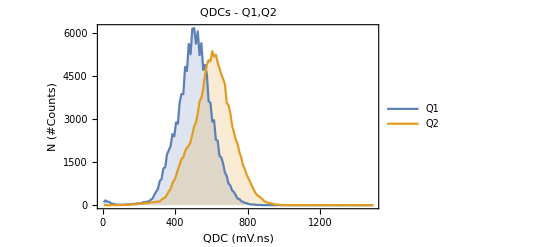

```mathematica
histbeg3=0;histlast3=1500;ChNum=4;binw3=10;
histdata=HistogramList[data[[1;;dimdata,5]],{histbeg3,histlast3,binw3}];
histdata2=HistogramList[data[[1;;dimdata,6]],{histbeg3,histlast3,binw3}];
ptdat=Table[{0,0},{k,1,Dimensions[histdata[[2]]][[1]]}];
ptdat2=Table[{0,0},{k,1,Dimensions[histdata2[[2]]][[1]]}];
For[i=1,i<=Dimensions[histdata[[2]]][[1]],i++,
ptdat[[i]][[1]]=histdata[[1]][[i]]+((-histdata[[1]][[1]]+histdata[[1]][[2]])/2);
ptdat[[i]][[2]]=histdata[[2]][[i]];
ptdat2[[i]][[1]]=histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2);
ptdat2[[i]][[2]]=histdata2[[2]][[i]];
];
Print["Total Events: ",Total[histdata[[2]]]];
ListLinePlot[{ptdat,ptdat2},PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"QDC (mV.ns)","N (#Counts)"},TicksStyle->Directive[FontSize->40],PlotLabel->"QDCs - Q1,Q2",PlotLegends->{"Q1","Q2"},Filling->Axis,ImageSize->{1000},TicksStyle->Directive[FontSize->40],LabelStyle->{18}]
```

```mathematica
Monitor[
Clear[data,histdata2];
data={};
For[runi=1,runi≤400,runi++,
If[runi≠ 20&&runi≠22,
data=Join[data,ReadList[StringJoin[AscDir,"\\",IntegerString[runNum,10,6],"\\",IntegerString[runNum,10,6],"_UCNdet_",IntegerString[runi,10,3],"_0001.fast.ascii"],metaStructure]];
];
];,ProgressIndicator[runi/10,ImageSize->{1000,100}]];
dimdata=Dimensions[data][[1]]
Dimensions[data]
histbeg3=0;histlast3=1500;ChNum=4;binw3=10;
dimdata=Dimensions[data][[1]];
cnt=Table[0,{k,1,dimdata}];j=1;
For[i=2,i≤dimdata,i++,
If[((Norm[data[[i]][[4]]-data[[i-1]][[4]]]<10000)&&(data[[i]][[3]]==data[[i-1]][[3]])),
cnt[[j]]=i;
j++;
];
];
bdlst=DeleteCases[cnt,0];
bddata=Part[data,bdlst];
gddata=DeleteCases[data,Alternatives@@bddata];
Print["Total Events: ",Dimensions[data][[1]]];
Print["Bad Events: ",Dimensions[bddata][[1]]," , Good Events: ",Dimensions[gddata][[1]]," , Total Events: ",Dimensions[bddata][[1]]+Dimensions[gddata][[1]]];
(**)
gddimdata=Dimensions[gddata][[1]];bddimdata=Dimensions[bddata][[1]];
(**)
histdatagd=HistogramList[gddata[[1;;gddimdata,5]],{histbeg3,histlast3,binw3}];
histdatagd2=HistogramList[gddata[[1;;gddimdata,6]],{histbeg3,histlast3,binw3}];
histdatabd=HistogramList[gddata[[1;;bddimdata,5]],{histbeg3,histlast3,binw3}];
histdatabd2=HistogramList[gddata[[1;;bddimdata,6]],{histbeg3,histlast3,binw3}];
(**)
ptdatgd=Table[{0,0},{k,1,Dimensions[histdatagd[[2]]][[1]]}];
ptdatgd2=Table[{0,0},{k,1,Dimensions[histdatagd2[[2]]][[1]]}];
For[i=1,i<=Dimensions[histdatagd[[2]]][[1]],i++,
ptdatgd[[i]][[1]]=histdatagd[[1]][[i]]+((-histdatagd[[1]][[1]]+histdatagd[[1]][[2]])/2);
ptdatgd[[i]][[2]]=histdatagd[[2]][[i]];
ptdatgd2[[i]][[1]]=histdatagd2[[1]][[i]]+((-histdatagd2[[1]][[1]]+histdatagd2[[1]][[2]])/2);
ptdatgd2[[i]][[2]]=histdatagd2[[2]][[i]];
];
(**)
ptdatbd=Table[{0,0},{k,1,Dimensions[histdatabd[[2]]][[1]]}];
ptdatbd2=Table[{0,0},{k,1,Dimensions[histdatabd2[[2]]][[1]]}];
For[i=1,i<=Dimensions[histdatabd[[2]]][[1]],i++,
ptdatbd[[i]][[1]]=histdatabd[[1]][[i]]+((-histdatabd[[1]][[1]]+histdatabd[[1]][[2]])/2);
ptdatbd[[i]][[2]]=histdatabd[[2]][[i]];
ptdatbd2[[i]][[1]]=histdatabd2[[1]][[i]]+((-histdatabd2[[1]][[1]]+histdatabd2[[1]][[2]])/2);
ptdatbd2[[i]][[2]]=histdatabd2[[2]][[i]];
];
(**)
bdlst
TableForm[Table[data[[bdlst[[k]]-1]],{k,1,Dimensions[bdlst][[1]]}]]
TableForm[Table[data[[bdlst[[k]]]],{k,1,Dimensions[bdlst][[1]]}]]
TableForm[Table[data[[bdlst[[k]]+1]],{k,1,Dimensions[bdlst][[1]]}]]
```

ReadList::readn: Invalid real number found when reading from "C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata\\011369\\011369_UCNdet_011_0001.fast.ascii".

ReadList::readn: Invalid real number found when reading from "C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata\\011369\\011369_UCNdet_046_0001.fast.ascii".

ReadList::readn: Invalid real number found when reading from "C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata\\011369\\011369_UCNdet_117_0001.fast.ascii".

General::stop: Further output of ReadList :: readn will be suppressed during this calculation.

85328

{85328}

Part::partd: Part specification $Failed ⟦ 4 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 3 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 4 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Total Events: 85328

Bad Events: 3 , Good Events: 85325 , Total Events: 85328

Part::partd: Part specification {{1844., "QDC_X3", 13., 1.48852×10^9, 21.006, 275.775, 30.488}, {3625., "QDC_X3", 18., 2.25681×10^9, 60.684, 974.074, 66.373}, {3627., "QDC_X3", 5., 2.25681×10^9, 31.509, 208.454, 32.968}, {3629., "QDC_X3", 6., 2.25681×10^9, 436.455, 2613.33, 440.831}, {3630., "QDC_X3", 9., 2.25681×10^9, 42.012, 246.527, 39.094}, {3631., "QDC_X3", 3., 2.25681×10^9, 80.522, 903.325, 77.751}, « 40 », {25312., "QDC_X3", 17., 1.16157×10^10, 1416.73, 1482.15, 2282.2}, {25313., "QDC_X3", 13., 1.16157×10^10, 1850.85, 1896.8, 3192.6}, {25314., "QDC_X3", 19., 1.16157×10^10, 1606.95, 1663.62, 2751.33}, {25315., "QDC_X3", 4., 1.16157×10^10, 837.9, 875.463, 1635.98}, « 85275 »} ⟦ 1 ;; 85325, 5 ⟧ is longer than depth of object.

HistogramList::ldata: {{1844., "QDC_X3", 13., 1.48852×10^9, 21.006, 275.775, 30.488}, {3625., "QDC_X3", 18., 2.25681×10^9, 60.684, 974.074, 66.373}, {3627., "QDC_X3", 5., 2.25681×10^9, 31.509, 208.454, 32.968}, {3629., "QDC_X3", 6., 2.25681×10^9, 436.455, 2613.33, 440.831}, {3630., "QDC_X3", 9., 2.25681×10^9, 42.012, 246.527, 39.094}, {3631., "QDC_X3", 3., 2.25681×10^9, 80.522, 903.325, 77.751}, « 40 », {25312., "QDC_X3", 17., 1.16157×10^10, 1416.73, 1482.15, 2282.2}, {25313., "QDC_X3", 13., 1.16157×10^10, 1850.85, 1896.8, 3192.6}, {25314., "QDC_X3", 19., 1.16157×10^10, 1606.95, 1663.62, 2751.33}, {25315., "QDC_X3", 4., 1.16157×10^10, 837.9, 875.463, 1635.98}, « 85275 »} ⟦ 1 ;; 85325, 5 ⟧ is not a valid dataset or list of datasets.

Part::partd: Part specification {{1844., "QDC_X3", 13., 1.48852×10^9, 21.006, 275.775, 30.488}, {3625., "QDC_X3", 18., 2.25681×10^9, 60.684, 974.074, 66.373}, {3627., "QDC_X3", 5., 2.25681×10^9, 31.509, 208.454, 32.968}, {3629., "QDC_X3", 6., 2.25681×10^9, 436.455, 2613.33, 440.831}, {3630., "QDC_X3", 9., 2.25681×10^9, 42.012, 246.527, 39.094}, {3631., "QDC_X3", 3., 2.25681×10^9, 80.522, 903.325, 77.751}, « 40 », {25312., "QDC_X3", 17., 1.16157×10^10, 1416.73, 1482.15, 2282.2}, {25313., "QDC_X3", 13., 1.16157×10^10, 1850.85, 1896.8, 3192.6}, {25314., "QDC_X3", 19., 1.16157×10^10, 1606.95, 1663.62, 2751.33}, {25315., "QDC_X3", 4., 1.16157×10^10, 837.9, 875.463, 1635.98}, « 85275 »} ⟦ 1 ;; 85325, 6 ⟧ is longer than depth of object.

HistogramList::ldata: {{1844., "QDC_X3", 13., 1.48852×10^9, 21.006, 275.775, 30.488}, {3625., "QDC_X3", 18., 2.25681×10^9, 60.684, 974.074, 66.373}, {3627., "QDC_X3", 5., 2.25681×10^9, 31.509, 208.454, 32.968}, {3629., "QDC_X3", 6., 2.25681×10^9, 436.455, 2613.33, 440.831}, {3630., "QDC_X3", 9., 2.25681×10^9, 42.012, 246.527, 39.094}, {3631., "QDC_X3", 3., 2.25681×10^9, 80.522, 903.325, 77.751}, « 40 », {25312., "QDC_X3", 17., 1.16157×10^10, 1416.73, 1482.15, 2282.2}, {25313., "QDC_X3", 13., 1.16157×10^10, 1850.85, 1896.8, 3192.6}, {25314., "QDC_X3", 19., 1.16157×10^10, 1606.95, 1663.62, 2751.33}, {25315., "QDC_X3", 4., 1.16157×10^10, 837.9, 875.463, 1635.98}, « 85275 »} ⟦ 1 ;; 85325, 6 ⟧ is not a valid dataset or list of datasets.

{370,40243,77132}

226570. | QDC_X3 | 13. | 9.85531×10^10 | 451.626 | 546.079 | 487.073
207301. | QDC_X3 | 14. | 9.02614×10^10 | 675.688 | 722.295 | 967.874
226797. | QDC_X3 | 11. | 9.86977×10^10 | 61.851 | 729.078 | 71.77

226572. | QDC_X3 | 13. | 9.85531×10^10 | 27.424 | 88.837 | 39.386
207302. | QDC_X3 | 14. | 9.02614×10^10 | 367.603 | 402.539 | 533.753
226798. | QDC_X3 | 11. | 9.86977×10^10 | 74.688 | 125.379 | 78.626

226688. | QDC_X3 | 6. | 9.85999×10^10 | 45.513 | 518.582 | 41.72
208044. | QDC_X3 | 8. | 9.0582×10^10 | 53.682 | 334.927 | 63.018
227584. | QDC_X3 | 1. | 9.90373×10^10 | 37.344 | 514.789 | 37.635

```mathematica
Norm[-190]
```

190

Total good Events: 131555

Total bad Events: 1990

First::normal: Nonatomic expression expected at position 1 in First[Automatic].

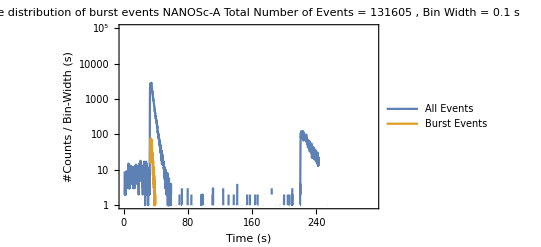

```mathematica
Print["Total good Events: ",Total[histdatagd[[2]]]];
(*ListLinePlot[{ptdatgd,ptdatgd2},PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"QDC (mV.ns)","N (#Counts)"},TicksStyle->Directive[FontSize->40],PlotLabel->"Filtered QDCs - Q1,Q2",PlotLegends->{"Q2","Q1"},Filling->Axis,ImageSize->{1000},TicksStyle->Directive[FontSize->40],LabelStyle->{18}]*)
(**)
Print["Total bad Events: ",Total[histdatabd[[2]]]];
(*ListLinePlot[{ptdatbd,ptdatbd2},PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"QDC (mV.ns)","N (#Counts)"},TicksStyle->Directive[FontSize->40],PlotLabel->"Burst QDCs - Q1,Q2",PlotLegends->{"Q2","Q1"},Filling->Axis,ImageSize->{1000},TicksStyle->Directive[FontSize->40],LabelStyle->{18}]*)
histbeg=100000000;histlast=302100000000;binw=100000000;
hst0=HistogramList[data[[2;;gddimdata,4]],{histbeg,histlast,binw}];
hst=HistogramList[gddata[[2;;gddimdata,4]],{histbeg,histlast,binw}];
hst2=HistogramList[bddata[[2;;bddimdata,4]],{histbeg,histlast,binw}];
ListLogPlot[{Transpose[{hst0[[1]][[1;;(histlast-histbeg)/binw]]/(10^9),hst0[[2]]}](*,Transpose[{hst[[1]][[1;;(histlast-histbeg)/binw]]/(10^9),hst[[2]]}]*),Transpose[{hst2[[1]][[1;;(histlast-histbeg)/binw]]/(10^9),hst2[[2]]}]},PlotRange->{{histbeg/(10^9),histlast/(10^9)+10},{0,100000}},Joined->True,Frame->True,FrameLabel->{"Time (s)","#Counts / Bin-Width (s)"},TicksStyle->Directive[FontSize->40],PlotLegends->{"All Events","Burst Events"},LabelStyle->{18},ImageSize->{1000},PlotLabel->StringJoin["Time distribution of burst events \n NANOSc-A \n Total Number of Events = ",ToString[Total[hst[[2]]]]," , Bin Width = ",ToString[N[binw/(10^9)]]," s"]]
```

```mathematica
ucnshutter=Table[0,{k,1,310,.1}];
ucnshutter[[260;;280]]=1;
ucnshutter[[2180;;2200]]=-1;
Print["Corr[Burst UCN Count, UCN Shutter State=1 (Opening)] = ",N[Correlation[hst2[[2]][[20;;199]],100ucnshutter[[1;;540;;3]]]]]
Print["Corr[Burst UCN Count, UCN Shutter State=-1 (Closing)] = ",N[Correlation[hst2[[2]][[220;;399]],100ucnshutter[[2001;;2540;;3]]]]]
```

Corr[Burst UCN Count, UCN Shutter State=1 (Opening)] = -0.0322102

Corr[Burst UCN Count, UCN Shutter State=-1 (Closing)] = 0.101716

First::normal: Nonatomic expression expected at position 1 in First[Automatic].

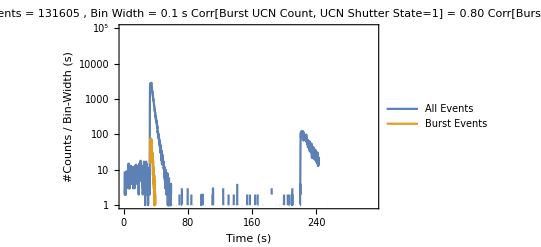
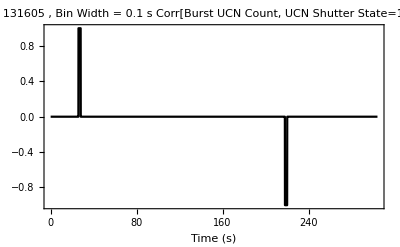

```mathematica
Overlay[{ListLogPlot[{Transpose[{hst0[[1]][[1;;(histlast-histbeg)/binw]]/(10^9),hst0[[2]]}](*,Transpose[{hst[[1]][[1;;(histlast-histbeg)/binw]]/(10^9),hst[[2]]}]*),Transpose[{hst2[[1]][[1;;(histlast-histbeg)/binw]]/(10^9),hst2[[2]]}]},ImagePadding->80,PlotRange->{{histbeg/(10^9),histlast/(10^9)+10},{0,100000}},Joined->True,FrameLabel->{"Time (s)","#Counts / Bin-Width (s)"},TicksStyle->Directive[FontSize->40],PlotLegends->{"All Events","Burst Events"},LabelStyle->{18},ImageSize->{1000},Filling->{True,True},PlotLabel->StringJoin["Time distribution of burst events \n Total Number of Events = ",ToString[Total[hst[[2]]]]," , Bin Width = ",ToString[N[binw/(10^9)]]," s \n Corr[Burst UCN Count, UCN Shutter State=1] = 0.80","\n Corr[Burst UCN Count, UCN Shutter State=-1] = 0.109"],Frame->{False,True,True,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}],
ListLinePlot[{Table[{k/10,ucnshutter[[k]]},{k,1,3040}]},ImagePadding->80,PlotStyle->Black,Frame->{True,False,False,True},FrameTicks->All,FrameStyle->{Automatic,Automatic,Automatic,Gray},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000},PlotLabel->StringJoin["Time distribution of burst events \n Total Number of Events = ",ToString[Total[hst[[2]]]]," , Bin Width = ",ToString[N[binw/(10^9)]]," s \n Corr[Burst UCN Count, UCN Shutter State=1] = 0.80","\n Corr[Burst UCN Count, UCN Shutter State=-1] = 0.109"],FrameLabel->{"Time (s)","","",Rotate["UCN Shutter State {1=Opening, -1=Closing}",180Degree]}]}]
```

## Leakage Current

Size of the file is = 5184

Size of the data set is = 300

First::normal: Nonatomic expression expected at position 1 in First[Automatic].

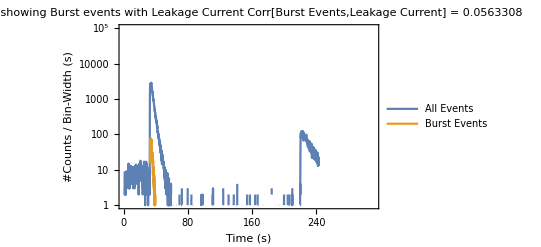
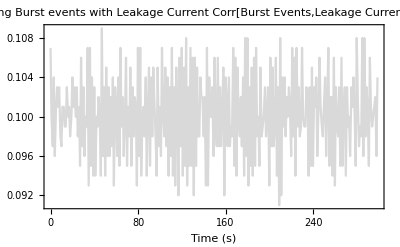

```mathematica
metaStructure3={Word,Real,Real,Real,Real,Real,Real};
lkgcur=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum,10,6],"\\",IntegerString[runNum,10,6],"X01-0_Leakage_current3.edm"],metaStructure3];
Print["Size of the file is = ",Dimensions[lkgcur][[1]]];
datac=Table[{0,0},{k,1,300}];
Print["Size of the data set is = ",Dimensions[datac][[1]]];
For[k=1,k≤300,k++,
datac[[k]]={(AbsoluteTime[lkgcur[[k]][[1]]]-AbsoluteTime[lkgcur[[1]][[1]]]),lkgcur[[k]][[2]]};
];
Overlay[{ListLogPlot[{Transpose[{hst0[[1]][[1;;(histlast-histbeg)/binw]]/(10^9),hst0[[2]]}](*,Transpose[{hst[[1]][[1;;(histlast-histbeg)/binw]]/(10^9),hst[[2]]}]*),Transpose[{hst2[[1]][[1;;(histlast-histbeg)/binw]]/(10^9),hst2[[2]]}]},Joined->True,ImagePadding->80,PlotRange->{{histbeg/(10^9),histlast/(10^9)+10},{0,100000}},Joined->True,FrameLabel->{"Time (s)","#Counts / Bin-Width (s)"},TicksStyle->Directive[FontSize->40],PlotLegends->{"All Events","Burst Events"},LabelStyle->{18},ImageSize->{1000},Filling->{True,True},PlotLabel->StringJoin["Plot showing Burst events with Leakage Current \n Corr[Burst Events,Leakage Current] = ",ToString[N[Correlation[hst2[[2]][[1;;300]],datac[[1;;300,2]]]]]],Frame->{False,True,True,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}],
ListLinePlot[{datac},ImagePadding->80,PlotStyle->LightGray,Frame->{True,False,False,True},FrameTicks->All,FrameStyle->{Automatic,Automatic,Automatic,Gray},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000},PlotLabel->StringJoin["Plot showing Burst events with Leakage Current \n Corr[Burst Events,Leakage Current] = ",ToString[N[Correlation[hst2[[2]][[1;;300]],datac[[1;;300,2]]]]]],FrameLabel->{"Time (s)","","",Rotate["Leakage Current (nA)",180Degree]}]}]
```

```mathematica
Correlation[hst2[[2]][[1;;300]],datac[[1;;300,2]]]
```

0.0563308